```mathematica
(* Set directory *)
SetDirectory[NotebookDirectory[]]
```

/Users/tanjona/Documents/Projects/optimBSFF

```mathematica
LabelPlot[fig_, xlab_, ylab_]:= Module[{out,xy},
Which[
xlab =="NA",
xy = Style[#, 18, Black, FontFamily->"Arial"]&/@ {ylab};
out = Labeled[fig,xy, {Left}, RotateLabel->True, Spacings->{1,1}],

ylab == "NA",
xy = Style[#, 18, Black, FontFamily->"Arial"]&/@ {xlab};
out = Labeled[fig,xy, {Bottom}, RotateLabel->True, Spacings->{1,1}],

xlab != "NA" && ylab != "NA",
xy = Style[#, 18, Black, FontFamily->"Arial"]&/@ {xlab,ylab};
out = Labeled[fig,xy, {Bottom, Left}, RotateLabel->True, Spacings->{0.75,0.75}]
];
out]
```

```mathematica
motif=Graphics[Line[Table[{{k,-1},{k+1,1}},{k,-2,2,.2}]],PlotRange-> 1];
motif=Graphics[{Line[{{-.1,-.1},{1.1,1.1}}],Line[{{-.1,1.1},{1.1,-.1}}]},ImageSize->32,PlotRange->{{0,1},{0,1}},PlotRangePadding->None];
```

```mathematica
(*
FAO data: 2023;

Maize;
yield = 1809.8 kg/ha; (estimated value);
production = 268062 t; (official figure);
area harvested = 148114 ha; (value imputed by a receiving agency);
price = 130.4 USD / t; (value imputed by a receiving agency);
Vincent = 1 300 000 MGA / t; 

Soybean; 
yield = 603.3 kg /ha; (estimated value);
production = 46.84 t; (value imputed by a receiving agency);
area harvest  = 78 ha; (value imputed by a receiving agency);
price = 352.4 USD / t; (value imputed by a receiving agency);
Vincent = 3 900 000 MGA / t; 


NPK Fertilizers: 9100 ar/kg NPK 112216;(https://www.fda.mg/dokany/index.php/produit/npk-11-22-16/ accessed 13 Mar 2026);
 So 1 kg N is 1000 * 9100 / 110 = 82727.2 ar for 1 kg of N
1 t frass at 3.46 %, = 34.6 kg N;
  priceNPK = 82727.2 * 34.6 / 4500 USD / 1t Frass;

Cattle manure Fertilizers: Mandoto 5809 ariary and Arivonimamo 16 158 arirary for one cart of 250 kg;
1 kg of cattle = 5809 / 250 * 1000 / 4500 USD = 5.16 USD / t
or ;
1 kg of cattle = 16158 / 250 * 1000 / 4500 USD = 14.36 USD / t
 
*)
```

```mathematica
1000 * 9100 / 110./4500
```

18.3838

```mathematica
9100/4500.
```

2.02222

```mathematica
82727.2 * 34.6 / 4500
```

636.08

```mathematica
(*Parameters from model fitting see R code*)
paramMaize = {asym -> 8.6027, r0 -> 0.6995, lrc-> -2.215, priceFAO -> 130.4, priceVincent ->  130.4 *2, yieldNational-> 1.8098};
paramSoy = {asym -> 4.086, r0 -> 2.335, lrc -> -2.211,priceFAO -> 352.4, priceVincent ->  352.4 *2, yieldNational-> 0.603};
priceNPK = 636.08; 
priceCMLow = 5.16;
priceCMHigh = 14.36;
priceMaizeMada = 1300000/4500.;
priceSoyMada = 3900000 / 4500.;

doseLocal = 43  /34.6(* using Cédrique 43 kg N/ha and 3.46% total N BSF, 34 kg N/t*)
(* 54545.5 * 34.6 / 4500 *)
doseFofifa = 3*43  /34.6(* three times local *)
```

1.24277

3.72832

```mathematica
(*yield as a function of dose in t/ha*)
yield[dose_]:= asym + (r0 - asym)Exp[-Exp[lrc] dose];

(* Optimal wrt to agronomic efficiency *)
yieldAgroEfficiency[dose_] := yield[dose] * (yield[dose] - yield[0])/dose;

(* 
compute the optimal doses for a given crop, frass price, and crop price; 
return  (1) the optimal dose, (2) net gain, and (3)the respective yield
*)
optimalDose[frassPrice_, cropPrice_, param_]:= Module[{temp, dd, res},
temp = FindMaximum[{( yield[dose] * cropPrice- dose * frassPrice) /.param,0 <= dose<= 30 },dose];
dd= dose /.temp[[2]];
res = {temp[[2,1]], netgain -> temp[[1]] , yield->yield[dd]/.param }//Association;
res];

(* Computes how much is the net gain with respect to total cost price of frass and the dose used *)
marginalVCR[dose_,frassPrice_, cropPrice_]:= Module[{},
rg = ((yield[dose] - yield[0])*cropPrice - (dose -0)* frassPrice )/ ((dose - 0) * frassPrice);
rg];

(* Computes how much is the net gain with respect to total cost price of frass and the dose used *)
relativeGain[dose_,frassPrice_, cropPrice_]:= Module[{},
rg = (yield[dose]*cropPrice - dose * frassPrice )/ (dose * frassPrice);
rg];
```

```mathematica
(*Finding doses that maximize the index*)
optimalAgroMaize = d/. FindMaximum[yieldAgroEfficiency[d]/.paramMaize, {d, 0.01,30}][[2]]
optimalAgroSoy = d/. FindMaximum[yieldAgroEfficiency[d]/.paramSoy, {d, 0.01,30}][[2]]
```

10.6096

2.58912

```mathematica
(* Dose required to reach national average *)
doseMaize = NSolve[{(yield[d] == yieldNational)/.paramMaize, d >=0},d ][[1,1]] //Values
doseSoy = NSolve[{(yield[d] == yieldNational) /.paramSoy, d >=0},d ][[1,1]] //Values
```

1.38694

Part::partw: Part 1 of {} does not exist.

Values::invrl: The argument {}⟦1,1⟧ is not a valid Association or a list of rules.

Values[{}⟦1,1⟧]

```mathematica
yield[30]/.{paramMaize, paramSoy}
```

{8.30371,4.02062}

```mathematica
(yield[30]/ yield[0])/.{paramMaize, paramSoy}
```

{11.8709,1.72189}

```mathematica
%/ {1.8, 0.6}
```

{4.61317,6.70103}

```mathematica
yield[1.2]/.{paramMaize, paramSoy}
```

{1.66976,2.55077}

```mathematica
yield[3.6]/.{paramMaize, paramSoy}
```

{3.26756,2.90583}

```mathematica
%/ {1.8, 0.6}
```

{1.81531,4.84305}

```mathematica
priceVincent /. {paramMaize, paramSoy}
```

{260.8,704.8}

### Marginal Value-Cost Ratio

#### Calculating number based on Cédrique’s dose

```mathematica
(* MCVR = 1 *)
frassPriceMaizeLocal1 = f/.NSolve[1 == marginalVCR[doseLocal,f, priceFAO]/.paramMaize, f][[1]];
frassPriceSoyLocal1 = f/.NSolve[1 == marginalVCR[doseLocal,f, priceFAO]/.paramSoy, f][[1]];

frassPriceMaizeLocalV1 = f/.NSolve[1 == marginalVCR[doseLocal,f, priceVincent]/.paramMaize, f][[1]];
frassPriceSoyLocalV1 = f/.NSolve[1 == marginalVCR[doseLocal,f, priceVincent]/.paramSoy, f][[1]];

Grid[{{"M = 1", "FAO", "Vincent"},{"Maize",frassPriceMaizeLocal1, frassPriceMaizeLocalV1},{"Soy",frassPriceSoyLocal1, frassPriceSoyLocalV1}}]
```

M = 1 | FAO | Vincent
Maize | 52.5974 | 105.195
Soy | 31.6102 | 63.2205

```mathematica
(* MCVR = 2 *)
frassPriceMaizeLocal2 = f/.NSolve[2 == marginalVCR[doseLocal,f, priceFAO]/.paramMaize, f][[1]];
frassPriceSoyLocal2  = f/.NSolve[2 == marginalVCR[doseLocal,f, priceFAO]/.paramSoy, f][[1]];

frassPriceMaizeLocalV2 = f/.NSolve[2 == marginalVCR[doseLocal,f, priceVincent]/.paramMaize, f][[1]];
frassPriceSoyLocalV2  = f/.NSolve[2 == marginalVCR[doseLocal,f, priceVincent]/.paramSoy, f][[1]];

Grid[{{"M = 2", "FAO", "Vincent"},{"Maize",frassPriceMaizeLocal2, frassPriceMaizeLocalV2},{"Soy",frassPriceSoyLocal2, frassPriceSoyLocalV2}}]
```

M = 2 | FAO | Vincent
Maize | 35.065 | 70.1299
Soy | 21.0735 | 42.147

```mathematica
(* MCVR = 3 *)
frassPriceMaizeLocal3 = f/.NSolve[3 == marginalVCR[doseLocal,f, priceFAO]/.paramMaize, f][[1]];
frassPriceSoyLocal3  = f/.NSolve[3 == marginalVCR[doseLocal,f, priceFAO]/.paramSoy, f][[1]];

frassPriceMaizeLocalV3 = f/.NSolve[3 == marginalVCR[doseLocal,f, priceVincent]/.paramMaize, f][[1]];
frassPriceSoyLocalV3  = f/.NSolve[3 == marginalVCR[doseLocal,f, priceVincent]/.paramSoy, f][[1]];

Grid[{{"M = 3", "FAO", "Vincent"},{"Maize",frassPriceMaizeLocal3, frassPriceMaizeLocalV3},{"Soy",frassPriceSoyLocal3, frassPriceSoyLocalV3}}]
```

M = 3 | FAO | Vincent
Maize | 26.2987 | 52.5974
Soy | 15.8051 | 31.6102

#### Calculating numbers based on Fofifa’s recommended dose

```mathematica
(* MCVR = 1 *)
frassPriceMaizeFofifa1  = f/.NSolve[1 == marginalVCR[doseFofifa,f, priceFAO]/.paramMaize, f][[1]];
frassPriceSoyFofifa1  = f/.NSolve[1 == marginalVCR[doseFofifa,f, priceFAO]/.paramSoy, f][[1]];

frassPriceMaizeFofifaV1 = f/.NSolve[1 == marginalVCR[doseFofifa,f, priceVincent]/.paramMaize, f][[1]];
frassPriceSoyFofifaV1  = f/.NSolve[1 == marginalVCR[doseFofifa,f, priceVincent]/.paramSoy, f][[1]];

Grid[{{"M = 1", "FAO", "Vincent"},{"Maize",frassPriceMaizeFofifa1, frassPriceMaizeFofifaV1},{"Soy",frassPriceSoyFofifa1, frassPriceSoyFofifaV1}}]
```

M = 1 | FAO | Vincent
Maize | 46.2073 | 92.4147
Soy | 27.7562 | 55.5123

```mathematica
(* MCVR = 2 *)
frassPriceMaizeFofifa2= f/.NSolve[2 == marginalVCR[doseFofifa,f, priceFAO]/.paramMaize, f][[1]];
frassPriceSoyFofifa2  = f/.NSolve[2 == marginalVCR[doseFofifa,f, priceFAO]/.paramSoy, f][[1]];

frassPriceMaizeFofifaV2 = f/.NSolve[2 == marginalVCR[doseFofifa,f, priceVincent]/.paramMaize, f][[1]];
frassPriceSoyFofifaV2  = f/.NSolve[2 == marginalVCR[doseFofifa,f, priceVincent]/.paramSoy, f][[1]];

Grid[{{"M = 2", "FAO", "Vincent"},{"Maize",frassPriceMaizeFofifa2, frassPriceMaizeFofifaV2},{"Soy",frassPriceSoyFofifa2, frassPriceSoyFofifaV2}}]
```

M = 2 | FAO | Vincent
Maize | 30.8049 | 61.6098
Soy | 18.5041 | 37.0082

```mathematica
(* MCVR = 3 *)
frassPriceMaizeFofifa3= f/.NSolve[3 == marginalVCR[doseFofifa,f, priceFAO]/.paramMaize, f][[1]];
frassPriceSoyFofifa3  = f/.NSolve[3 == marginalVCR[doseFofifa,f, priceFAO]/.paramSoy, f][[1]];

frassPriceMaizeFofifaV3 = f/.NSolve[3 == marginalVCR[doseFofifa,f, priceVincent]/.paramMaize, f][[1]];
frassPriceSoyFofifaV3  = f/.NSolve[3 == marginalVCR[doseFofifa,f, priceVincent]/.paramSoy, f][[1]];

Grid[{{"M = 3", "FAO", "Vincent"},{"Maize",frassPriceMaizeFofifa3, frassPriceMaizeFofifaV3},{"Soy",frassPriceSoyFofifa3, frassPriceSoyFofifaV3}}]
```

M = 3 | FAO | Vincent
Maize | 23.1037 | 46.2073
Soy | 13.8781 | 27.7562

### MVCR based on price or dose

```mathematica
marginalVCR[ doseLocal , frassPriceSoyLocal1, priceFAO]/.paramMaize
```

2.32787

```mathematica
marginalVCR[ doseFofifa , frassPriceSoyLocal1, priceFAO]/.paramMaize
```

1.92357

```mathematica
marginalVCR[doseLocal , frassPriceSoyLocal3, priceFAO]/.paramMaize
```

5.65575

```mathematica
marginalVCR[ doseFofifa , frassPriceSoyLocal3, priceFAO]/.paramMaize
```

4.84714

```mathematica
marginalVCR[doseLocal , frassPriceSoyFofifa3, priceFAO]/.paramMaize
```

6.57993

```mathematica
marginalVCR[ doseFofifa , frassPriceSoyFofifa3, priceFAO]/.paramMaize
```

5.65904

```mathematica
FindY[dose_, mvcr_, param_] := Module[{res},
res = f/. NSolve[mvcr == marginalVCR[dose,f, priceFAO]/.param, f][[1]];
res]
```

```mathematica
FindY[12,3, paramMaize]
```

15.6763

#### Figure

```mathematica
is = 300;ls = Directive[14,Black,FontFamily->"Arial"];
```

```mathematica
fMaizeFAO = ContourPlot[
marginalVCR[dose, f, priceFAO] /. paramMaize, {dose, 0.1, 30},{f,1, 60},
ScalingFunctions->{None, None, None},
PlotRange->{0.99, 2000}, Contours->{1,2,3,10,50}, ContourShading->None,ContourLabels->(Text[Style[Framed[#3, FrameMargins->1],10],{12,FindY[12, #3, paramMaize]},Background->White]&),ClippingStyle->PatternFilling[motif,ImageScaled[1/40]],
GridLines->
{{{doseLocal,Directive[Gray,Dashed]},{doseFofifa,Directive[Gray]}}, 
{ {frassPriceMaizeLocal1,Directive[Red, Dashed, AbsoluteThickness[1.5]]}, 
{frassPriceMaizeLocal3,Directive[Red, Dashed, AbsoluteThickness[3]]},
{frassPriceMaizeFofifa1,Directive[Red ,AbsoluteThickness[1.5]]},{frassPriceMaizeFofifa3,Directive[Red,  AbsoluteThickness[3]]}}},
GridLinesStyle->Directive[Red,Thick],Method->{"GridLinesInFront"->False},ImageSize->is, LabelStyle->ls]
```

-Graphics-

```mathematica
fMaizeVincent = ContourPlot[
marginalVCR[dose, f, priceVincent] /. paramMaize, {dose, 0.1, 30},{f,1, 60},
ScalingFunctions->{None, None, None},
PlotRange->{0.99, 2000}, Contours->{1,2,3,10,50}, ContourShading->None,ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),ClippingStyle->PatternFilling[motif,ImageScaled[1/40]],
GridLines->
{{{doseLocal,Directive[Gray,Dashed]},{doseFofifa,Directive[Gray]}},None},
GridLinesStyle->Directive[Red,Thick],ImageSize->is,LabelStyle->ls]
```

-Graphics-

```mathematica
fSoyFAO = ContourPlot[
marginalVCR[dose, f, priceFAO] /. paramSoy, {dose, 0.1, 30},{f,1, 60},
ScalingFunctions->{None, None, None},
PlotRange->{0.99, 2000}, Contours->{1,2,3,10,50}, ContourShading->None,ContourLabels->(Text[Style[Framed[#3, FrameMargins->1],10],{5.5,FindY[5.5, #3, paramSoy]},Background->White]&),ClippingStyle->PatternFilling[motif,ImageScaled[1/40]],
GridLines->
{{{doseLocal,Directive[Gray,Dashed]},{doseFofifa,Directive[Gray]}}, 
{ {frassPriceSoyLocal1,Directive[Red, Dashed, AbsoluteThickness[1.5]]}, 
{frassPriceSoyLocal3,Directive[Red, Dashed, AbsoluteThickness[3]]},
{frassPriceSoyFofifa1,Directive[Red ,AbsoluteThickness[1.5]]},{frassPriceSoyFofifa3,Directive[Red,  AbsoluteThickness[3]]}}},
GridLinesStyle->Directive[Magenta,Thick],Method->{"GridLinesInFront"->False},ImageSize->is,LabelStyle->ls]
```

-Graphics-

```mathematica
fSoyVincent = ContourPlot[
marginalVCR[dose, f, priceVincent] /. paramSoy, {dose, 0.1, 30},{f,1, 60},
ScalingFunctions->{None, None, None},
PlotRange->{0.99, 2000}, Contours->{1,2,3,10,50}, ContourShading->None,ContourLabels->(Text[Framed[#3] ,{#1,#2},Background->White]&),ClippingStyle->PatternFilling[motif,ImageScaled[1/40]],
GridLines->
{{{doseLocal,Directive[Gray,Dashed]},{doseFofifa,Directive[Gray]}}, None},
GridLinesStyle->Directive[Magenta,Thick],Method->{"GridLinesInFront"->False},ImageSize->is,LabelStyle->ls]
```

-Graphics-

```mathematica
fMVCR = Labeled[
Grid[{Style[#, 18, Black, FontFamily->"Arial"]&/@{"A                                                               ", "B                                                               "},{fMaizeFAO, fSoyFAO}},
 Spacings->2], Style[#, 18, Black, FontFamily->"Arial"]&/@{"Fertilizer application rate (t ha^-1 )", "Frass price (USD t^-1)"},{Bottom, Left}, RotateLabel->True]
```

A                                                                | B                                                               
-Graphics- | -Graphics-Fertilizer application rate (t ha^-1 )Frass price (USD t^-1)

```mathematica
Export["figMath/fig-MVCR.png", fMVCR, ImageResolution->400]
```

figMath/fig-MVCR.png

```mathematica
fMVCR = Labeled[
Grid[{Style[#, 18, Black, FontFamily->"Arial"]&/@{"A                                                               ", "B                                                               "},{fMaizeFAO, fSoyFAO},
Style[#, 18, Black, FontFamily->"Arial"]&/@{"C                                                               ", "D                                                               "},{fMaizeVincent, fSoyVincent}},
 Spacings->2], Style[#, 18, Black, FontFamily->"Arial"]&/@{"Fertilizer application rate (t ha^-1 )", "Frass price (USD t^-1)"},{Bottom, Left}, RotateLabel->True]
```

A                                                                | B                                                               
-Graphics- | -Graphics-
C                                                                | D                                                               
-Graphics- | -Graphics-Fertilizer application rate (t ha^-1 )Frass price (USD t^-1)

```mathematica
Export["figMath/fig-MVCR.png", fMVCR, ImageResolution->400]
```

figMath/fig-MVCR.png

### Relative gain

```mathematica
rgMaize10 = relativeGain[optimalAgroMaize, priceNPK/10 , priceFAO]/.paramMaize
rgMaize100 = relativeGain[optimalAgroMaize,priceNPK/100 , priceFAO]/.paramMaize
```

0.913292

18.1329

```mathematica
rgSoy10 = relativeGain[optimalAgroSoy, priceNPK/10 , priceFAO]/.paramSoy
rgSoy100 = relativeGain[optimalAgroSoy,priceNPK/100 , priceFAO]/.paramSoy
```

7.9515

88.515

```mathematica
fMRelGain1 = ContourPlot[
relativeGain[dose, f, priceFAO] /. paramMaize, {dose, 0.1, 30},{f,1, 100},
ScalingFunctions->{None, "Log", None},
PlotRange->{0.99, 2000}, Contours->{1,2,3,10,50}, ContourShading->None,ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),ClippingStyle->PatternFilling[motif,ImageScaled[1/40]],
GridLines->
{{optimalAgroMaize}, 
{{priceNPK/ 10,Directive[Red, Dashed]}, {priceNPK/100,Directive[Red, Thin]}}},
GridLinesStyle->Directive[Red,Thin]]
```

-Graphics-

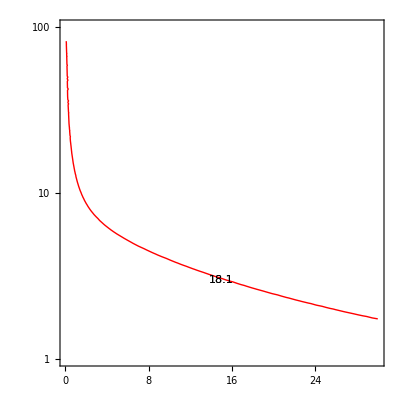

```mathematica
fMRelGain2 = ContourPlot[relativeGain[dose, f, 130]/. paramMaize, {dose, 0.1, 30},{f,1, 100},
ScalingFunctions->{None, "Log", None}, Contours->{rgMaize100}, ContourShading->None,ContourStyle->Directive[Red,Thick],ContourLabels->(Text[Framed[Style[Round[#3,0.1], Red,Bold, 16], FrameStyle->Red],{15,Log[3]},Background->White]&)]
```

```mathematica
fMRelGain = Show[fMRelGain1, fMRelGain2,ImageSize ->300,LabelStyle->Directive[Black, 16, FontFamily->"Arial"]]
```

-Graphics-

```mathematica
fSRelGain1 = ContourPlot[
relativeGain[dose, f, priceFAO] /. paramSoy, {dose, 0.1, 30},{f,1, 100},
ScalingFunctions->{None, "Log", None},
PlotRange->{0.99, 20000}, Contours->{1,2,3,10,50}, ContourShading->None,ContourLabels->(Text[Framed[#3],{#1,#2},Background->White]&),ClippingStyle->PatternFilling[motif,ImageScaled[1/40]],
GridLines->
{{optimalAgroSoy}, 
{{priceNPK/ 10,Directive[Red, Dashed]}, {priceNPK/100,Directive[Red, Thin]}}},
GridLinesStyle->Directive[Red,Thin]]
```

-Graphics-

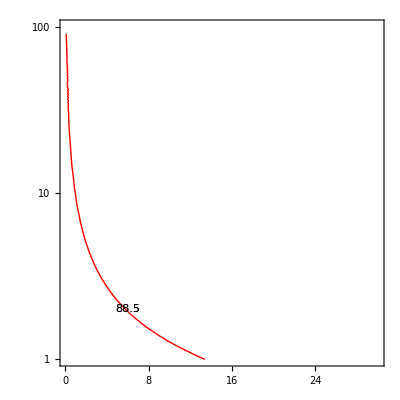

```mathematica
fSRelGain2 = ContourPlot[relativeGain[dose, f, priceFAO]/. paramSoy, {dose, 0.1, 30},{f,1, 100},
ScalingFunctions->{None, "Log", None}, Contours->{rgSoy100}, ContourShading->None,ContourStyle->Directive[Red,Thick],ContourLabels->(Text[Framed[Style[Round[#3,0.1], Red,Bold, 16], FrameStyle->Red],{6,Log[2]},Background->White]&)]
```

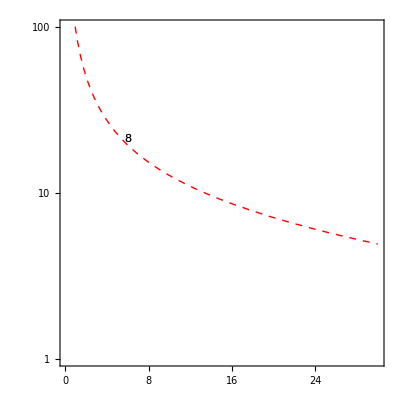

```mathematica
fSRelGain3 = ContourPlot[relativeGain[dose, f, priceFAO]/. paramSoy, {dose, 0.1, 30},{f,1, 100},
ScalingFunctions->{None, "Log", None}, Contours->{rgSoy10}, ContourShading->None,ContourStyle->Directive[Red,Thick,Dashed],ContourLabels->(Text[Framed[Style[Round[#3,1], Red,Bold, 16], FrameStyle->Red],{6,Log[21]},Background->White]&)]
```

```mathematica
fSRelGain = Show[fSRelGain1, fSRelGain2, fSRelGain3,ImageSize->300,LabelStyle->Directive[Black, 16, FontFamily->"Arial"]]
```

-Graphics-

```mathematica
fRElGain = Labeled[
Grid[{Style[#, 18, Black, FontFamily->"Arial"]&/@{"A                                                               ", "B                                                               "},{fMRelGain, fSRelGain}}, Spacings->2], Style[#, 18, Black, FontFamily->"Arial"]&/@{"Fertilizer dose (t ha^-1 )", "Frass price (USD t^-1)"},{Bottom, Left}, RotateLabel->True]
```

A                                                                | B                                                               
-Graphics- | -Graphics-Fertilizer dose (t ha^-1 )Frass price (USD t^-1)

```mathematica
Export["/Users/tanjona/Documents/Projects/diego_katsaka/figMath/fig-relGain.png", fRElGain, ImageResolution->350]
```

/Users/tanjona/Documents/Projects/diego_katsaka/fig/fig-relGain.png

### Supp fig

```mathematica
priceNPK
```

636.08

```mathematica
priceFAO/.paramMaize
```

130.4

```mathematica
(* Image padding*)
ip = {{50,5},{50,10}};
```

```mathematica
fSuppMDose1 = ContourPlot[
Round[optimalDose[f, m, paramMaize][dose], 0.001], {f, 1,priceNPK }, {m, 0,450},  
Contours-> Range[0,29, 5], PlotRange->{0.1, 35}, PlotPoints->50, LabelStyle->Directive[Black, 16, FontFamily->"Arial"],GridLines->{{priceNPK},{priceFAO/.paramMaize}},GridLinesStyle->Directive[Thick, Dashed, Red],
ScalingFunctions->{"Log", None, None}, ColorFunction->GrayLevel, ClippingStyle->PatternFilling[motif,ImageScaled[1/40]]]
```

-Graphics-

```mathematica
doseMaize
```

0.898467

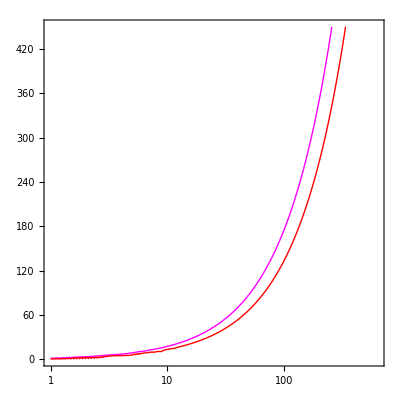

```mathematica
fSuppMDose2 = ContourPlot[Round[optimalDose[f, m, paramMaize][dose], 0.001], {f,1,priceNPK}, {m, 0, 450},  Contours-> {doseLocal,doseFofifa}, ScalingFunctions->{"Log", None, None},ContourShading->None, ContourStyle->{Directive[Red,Thick],Directive[Magenta,Thick]}]
```

```mathematica
fSuppMDose = Show[fSuppMDose1, fSuppMDose2, ImageSize -> {Automatic,350}, ImagePadding->ip]
```

-Graphics-

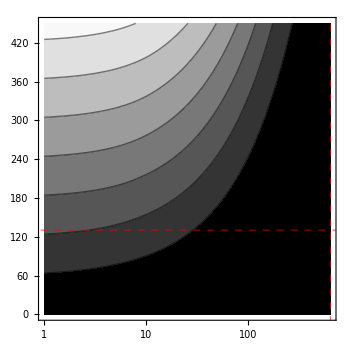

```mathematica
fSuppMGain = ContourPlot[Round[optimalDose[f, m, paramMaize][netgain], 0.001], {f,1,priceNPK}, {m, 0,450},  ContourLabels->Automatic, ScalingFunctions->{"Log", None, None},ColorFunction->GrayLevel ,PlotRange->{0.001, 4000},ClippingStyle->Red,LabelStyle->Directive[Black, 16, FontFamily->"Arial"],
GridLines->{{priceNPK},{priceFAO/.paramMaize}},GridLinesStyle->Directive[Thick, Dashed, Red], ImageSize->350,ImagePadding->ip]
```

```mathematica
fSuppSDose1 = ContourPlot[Round[optimalDose[f, m, paramSoy][dose], 0.001], {f, 1, priceNPK}, {m, 0, 1000},  Contours-> Range[0,29, 5], PlotRange->{0.1, 35}, PlotPoints->100,
PlotLegends->BarLegend[Automatic, LegendLabel->"Optimal dose (t ha^-1)", LegendMarkerSize->180],
GridLines->{{priceNPK},{priceFAO/.paramSoy}},GridLinesStyle->Directive[Thick, Dashed, Red], ScalingFunctions->{"Log", None, None}, ColorFunction->GrayLevel, ClippingStyle->PatternFilling[motif,ImageScaled[1/40]],LabelStyle->Directive[Black, 16, FontFamily->"Arial"], ImageSize->350]
```

-Graphics-

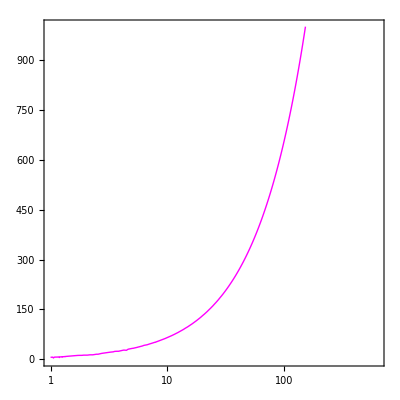

```mathematica
fSuppSDose2 = ContourPlot[Round[optimalDose[f, m, paramSoy][dose], 0.001], {f, 1, priceNPK}, {m, 0, 1000},  Contours-> { 2.04}, ScalingFunctions->{"Log", None, None},ContourShading->None, ContourStyle->{Directive[Magenta,Thick]}]
```

```mathematica
fSuppSDose = Show[fSuppSDose1, fSuppSDose2, ImageSize -> {Automatic,350}, ImagePadding->ip]
```

-Graphics-

```mathematica
fSuppSGain = ContourPlot[Max[Round[optimalDose[f, m, paramSoy][netgain], 0.001],0], {f, 1, priceNPK}, {m, 0, 1000},  PlotPoints->10,
PlotLegends->BarLegend[Automatic, LegendLabel->"Net gain (USD t^-1)", LegendMarkerSize->180],
GridLines->{{priceNPK},{priceFAO/.paramSoy}},GridLinesStyle->Directive[Thick, Dashed, Red],  ScalingFunctions->{"Log", None, None}, ColorFunction->GrayLevel,PlotRange->{0.001, 3600},LabelStyle->Directive[Black, 16, FontFamily->"Arial"], ImageSize->350,ImagePadding->ip]
```

-Graphics-

```mathematica
fSuppDoseGain = Labeled[Grid[{{fSuppMDose, fSuppMGain},{fSuppSDose, fSuppSGain}}//Transpose, Spacings->0.5], Style[#, 18, Black, FontFamily->"Arial"]&/@{"Frass price (USD t^-1)", "Yield price (USD t^-1)"},{Bottom, Left}, RotateLabel->True]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-Frass price (USD t^-1)Yield price (USD t^-1)

```mathematica
Export["figMath/figS-DoseGain.png", fSuppDoseGain, ImageResolution->350]
```

figMath/figS-DoseGain.png